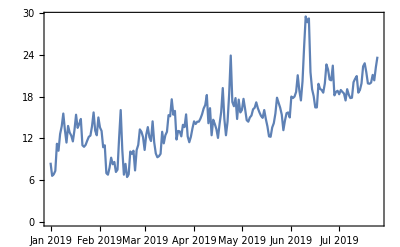

```mathematica
DateListPlot[WeatherData["Sunnyvale","MeanTemperature",{{2019,1,1},{2019,7,26},"Day"}],Joined->True]
```

```mathematica
WeatherData["Sunnyvale","Temperature","NonMetricValue"]
```

75.92 °F

```mathematica
WeatherData["Sunnyvale","MeanTemperature",{{2019,1,1},{2019,7,26},"Day"}]
```

TimeSeries[…]

```mathematica
datF=UnitConvert[%15[[2,1,1]],"DegreesFahrenheit"]
```

QuantityArray[…]

```mathematica
datC=%15[[2,1,1]]
```

QuantityArray[…]

```mathematica
UnitConvert[%15,"DegreesFahrenheit"]
```

TimeSeries[…]

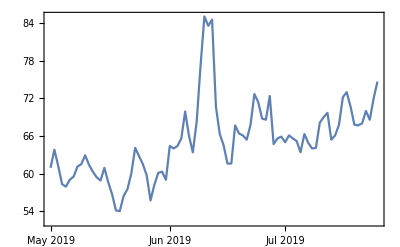

```mathematica
DateListPlot[UnitConvert[WeatherData["Sunnyvale","MeanTemperature",{{2019,5,1},{2019,7,31},"Day"}],"DegreesFahrenheit"]]
```

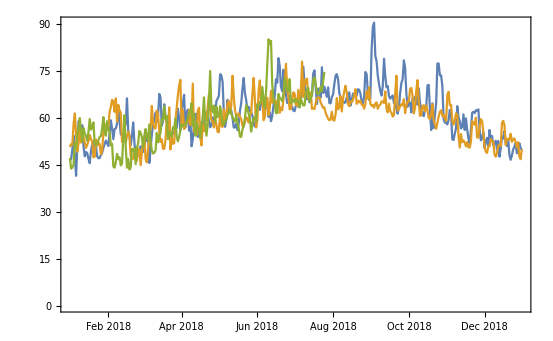

```mathematica
DateListPlot[{UnitConvert[WeatherData["Sunnyvale","MeanTemperature",{{2017,1,1},{2017,12,31},"Day"}],"DegreesFahrenheit"],UnitConvert[WeatherData["Sunnyvale","MeanTemperature",{{2018,1,1},{2018,12,31},"Day"}],"DegreesFahrenheit"],UnitConvert[WeatherData["Sunnyvale","MeanTemperature",{{2019,1,1},{2019,12,31},"Day"}],"DegreesFahrenheit"]}/. {2019->2018,2017->2018}]
```

```mathematica
dates=UnitConvert[WeatherData["Sunnyvale","MeanTemperature",{{2019,1,1},{2019,12,31},"Day"}],"DegreesFahrenheit"][[2]]
```

{{QuantityArray[…]},{TemporalData`DateSpecification[{2019,1,1,0,0,0.},{2019,7,25,0,0,0.},{1,Day}]},1,{Continuous,1},{Discrete,1},1,{ValueDimensions→1,DateFunction→Automatic,ResamplingMethod→{Interpolation,InterpolationOrder→1}}}

```mathematica
dates2=(AbsoluteTime[DateList[#]/.{2019->2018}])&/@dates;
```